```mathematica
(*Procedendo para o paper do Muga,vamos integrar psi(x,t)*V1(x) para encontrar a distribuição de probabilidade temporal-que eventualmente em x=0 será nossa condição inicial no STS-por isso,aqui temos nossa C.I.do STS definida em formato de função*)dndt[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+50)^2+2*1*t*(-50))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-50)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+50)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

```mathematica
dndtinterpol=FunctionInterpolation[Re[-dndt[t]],{t,10,60}]//Quiet (*Interpolando pro mathematica assumir uma forma funcionar polinomial e rodar a integral mais rápido*)
```

InterpolatingFunction[…]

```mathematica
NSolve[A*NIntegrate[dndtinterpol[t],{t,0,60}] == 1,A]
```

{{A→0.871875}}

```mathematica
dnintnorm [t_]:= 0.8718754956340197*dndtinterpol[t]
```

```mathematica
NIntegrate[dndtinterpol[t]*0.8718754956340197, {t,0,60}]
```

1.

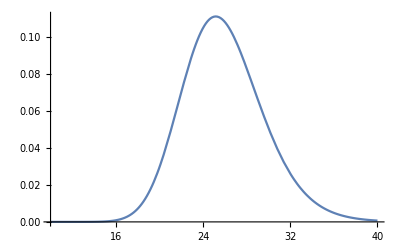

```mathematica
Plot[dnintnorm[t],{t,10,40},MaxRecursion->2](*Plot da distribuição temporal do Muga dndt em x=0,tudo funcionando exatamente como no paper*)
```

```mathematica
(*Agora,em ordem a preparar o plot do STS-primeiro como fazíamos antes,usando condição inicial temporal-*,vamos por o dndt como condição inicial)*)cepsilon[ϵ_]:=NIntegrate[ (1/Sqrt[Pi])*dnintnorm[t]*Exp[(I*ϵ*t)],{t,0,60}] 
Plot[ {Re[cepsilon[ϵ]], Im[cepsilon[ϵ]]},{ϵ,-10,10},MaxRecursion->3,PlotPoints->20,PlotRange->All, PlotLegends->Automatic] (*Plotando pra reconhecer limites interessantes de plot numérico para calcular o Cp temporal do STS*)
```

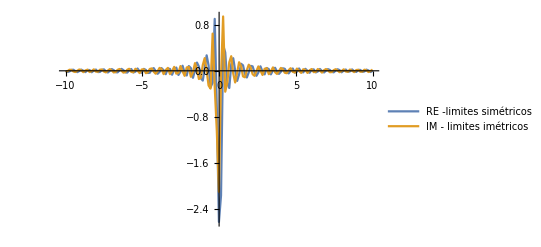

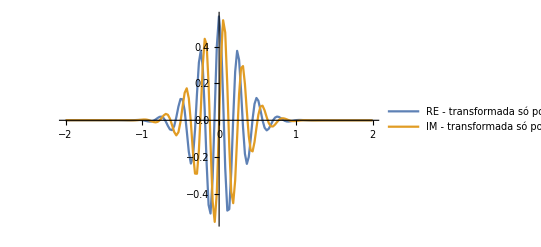

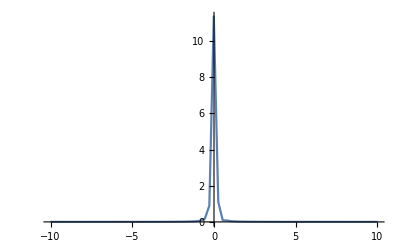

```mathematica
(*Plotando modulo ao quadrado das curvas anteriores com resolução baixa para agilizar para verificarmos o comportamento gaussiano*)Plot[Abs[cepsilon[ϵ]]^2, {ϵ,-10, 10},MaxRecursion->2,PlotPoints->20,PlotRange->All]
```

```mathematica
NIntegrate[Abs[cepsilon[ϵ]]^2,{ϵ,-10, 10}](*verificando normalização - as componentes negativas continuam causando algum problema*)
```

2.99705

```mathematica
(*Antes de rodar a interpolação para essa comparação, precisamos investigar o comportamento estranho de Ce. Sugestão de Eduardo é que a transf. deve agir sobre a função de onda, não sobre a distribuição de prob. Para concertar isso, vamos prosseguir de forma que*)
fourier[t_,α_]:= Sqrt[dnintnorm[t]]*Exp[I*α*t]
```

```mathematica
cepsilonwave[ϵ_]:=NIntegrate[ (1/Sqrt[2*Pi])*fourier[t,1]*Exp[(I*ϵ*t)],{t,0,60}] 
Plot[ {Re[cepsilonwave[ϵ]], Im[cepsilonwave[ϵ]]},{ϵ,-5,5},MaxRecursion->3,PlotPoints->20,PlotRange->All, PlotLegends->Automatic]
```

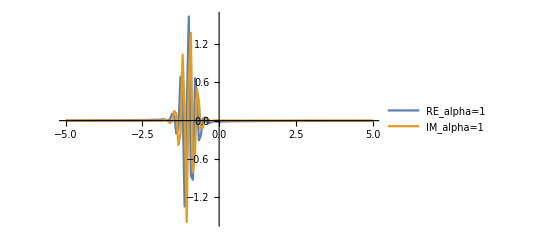
```mathematica
-Graphics-(*Números positivos para alpha no termo de oscilação fazem com que o C_epsilon fique inteiramente espelhado em termos negativos;Caso os limites de integração sejam ajustados para compreender esses valores, verifiquei que a densidade de probabilidade no STS se move tal qual está se movendo atualmente para valores negativos, só que com valores e direção espelhados.*)
```

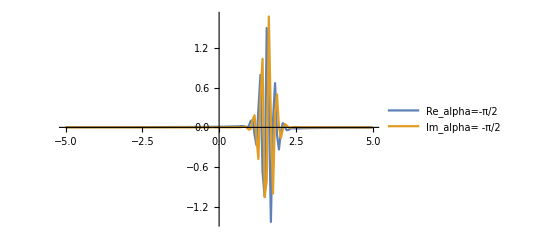

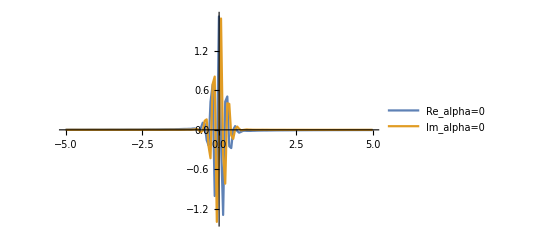
```mathematica
-Graphics-(*Perceba que se retirarmos o termo de oscilação, o C_{epsilon} volta a ter componentes negativos, que faz com que o STS não funcione centralizado corretamente lá no final, então não podemos igualar alpha a 0 a partir daqui.*)
```

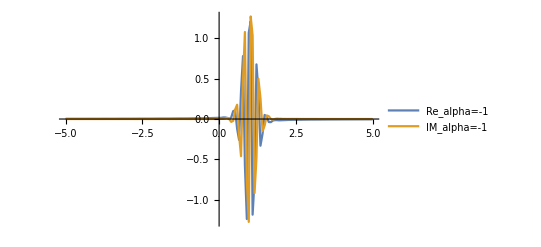

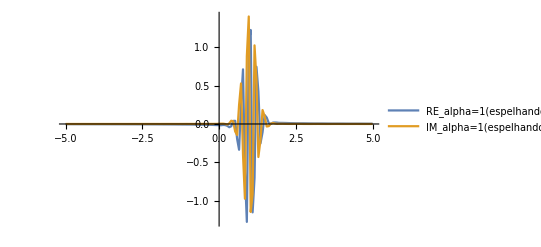

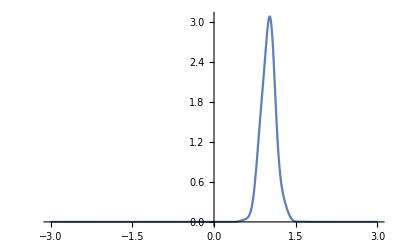

```mathematica
Plot[ Abs[cepsilonwave[ϵ]]^2,{ϵ,-3,3},MaxRecursion->5,PlotPoints->20,PlotRange->All, PlotLegends->Automatic]
```

```mathematica
NIntegrate[Abs[cepsilonwave[ϵ]]^2,{ϵ,0, 5}]
```

1.00702

```mathematica
cepsiloninterpol=FunctionInterpolation[cepsilonwave[ϵ],{ϵ,-5,5}] //Quiet(*Interpolando mais uma vez pra resolver a integral em tempo decente*)
```

InterpolatingFunction[…]

```mathematica
Plot[ {Re[cepsiloninterpol[ϵ]], Im[cepsiloninterpol[ϵ]]},{ϵ,-5,5},MaxRecursion->3,PlotPoints->20,PlotRange->All, PlotLegends->Automatic]
```

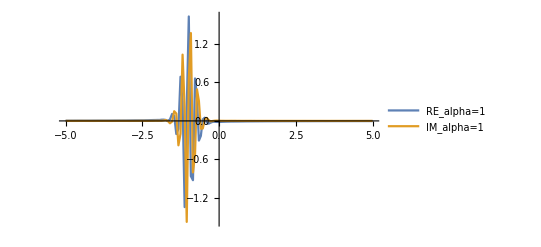

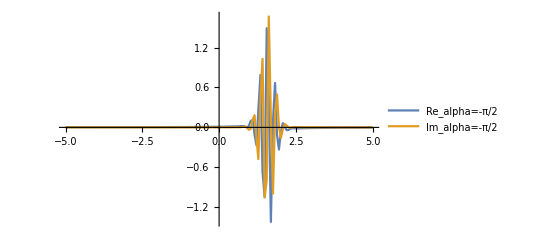

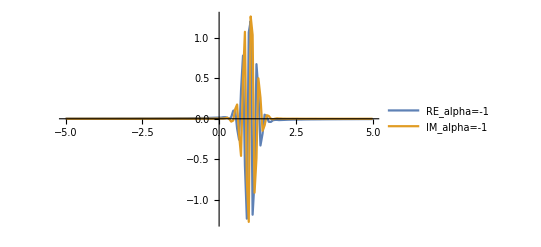

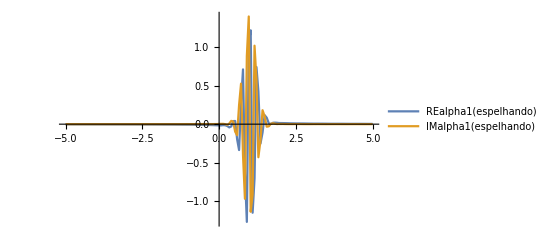

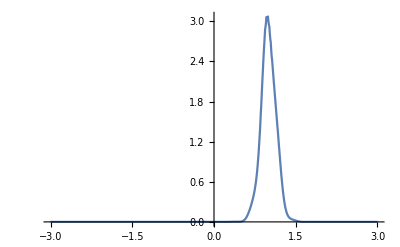

```mathematica
Plot[ Abs[cepsiloninterpol[ϵ]]^2,{ϵ,-3,3},  MaxRecursion->10,PlotPoints->50,PlotRange->All, PlotLegends->Automatic]
```

```mathematica
NIntegrate[Abs[cepsiloninterpol[ϵ]]^2,{ϵ,-3, 3}]
```

1.0003

```mathematica
cepsiloninterpoladjust[ϵ_]:=Piecewise[ {{0,ϵ<-5},{cepsiloninterpol[ϵ],-5<ϵ<5},{0,ϵ>5}}]
```

```mathematica
Plot[ {Re[cepsiloninterpoladjust[ϵ]], Im[cepsiloninterpoladjust[ϵ]]},{ϵ,-5,5},MaxRecursion->3,PlotPoints->20,PlotRange->All, PlotLegends->Automatic]
```

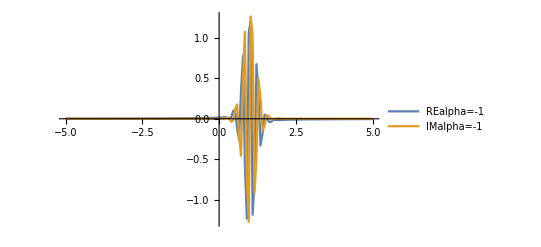

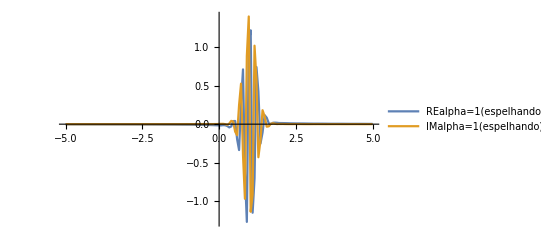

```mathematica
Plot[ Abs[cepsiloninterpoladjust[ϵ]]^2,{ϵ,-3,3},  MaxRecursion->10,PlotPoints->50,PlotRange->All, PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*Agora,adicionando o propagador e voltando a transformada de Fourier tal qual fizemos anteriormente em schrodinger para obter a distribuição temporal STS*)sts[x_,t_]:=NIntegrate[1/(Sqrt[2*Pi])*cepsiloninterpoladjust[ϵ]*1/(ϵ^(1/4))*Exp[-(I*(ϵ*t))]*Exp[(I*x*Sqrt[ϵ])],{ϵ,0,50}]
```

```mathematica
sts[0,2](*teste só pra ver se não diverge num valor arbitrário aqui*)
```

-0.0090931-0.00493536 ⅈ

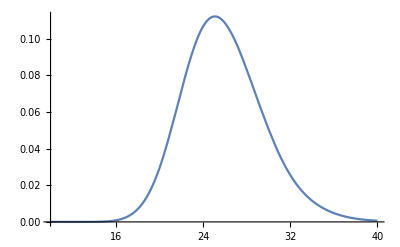

```mathematica
Plot[Abs[sts[0,t]]^2,{t,10,40},PlotRange->All,MaxRecursion->2,PlotPoints->40](*aqui, verificando se o modelo está compatível com a condição inicial do muga que queríamos a príncípio - aquela gaussiana "deformada" com cauda na direita centrada em 25*)
```

```mathematica
Plot[{Abs[sts[0,t]]^2,dnintnorm[t]},{t,10,40},PlotLegends->Automatic](*gráfico pra validar todo o processo até aqui*)
```

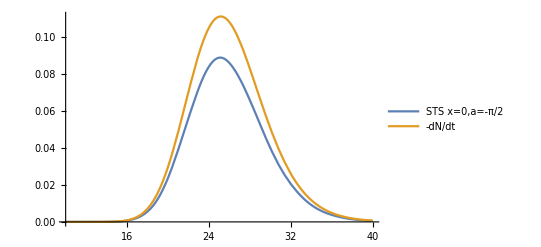

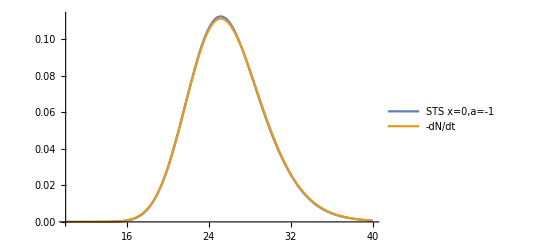

```mathematica
dndtx10[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+60)^2+2*1*t*(-60))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+60)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-60)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+60)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

```mathematica
dn10=FunctionInterpolation[Re[-dndtx10[t]],{t,10,70}]//Quiet
```

InterpolatingFunction[…]

```mathematica
NSolve[A*NIntegrate[dn10[t],{t,10,50}] == 1,A]
```

{{A→0.869013}}

```mathematica
dnorm10 [t_]:= 0.8690131472799185*dn10[t]
```

```mathematica
Plot[{1.15*Abs[sts[10,t]]^2,dnorm10[t]},{t,15,50},PlotLegends->Automatic]
```

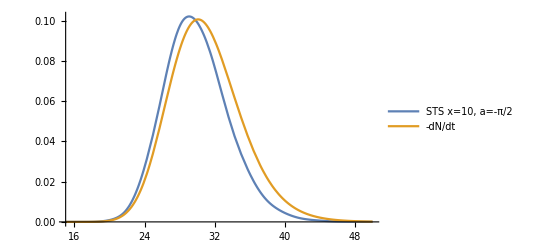

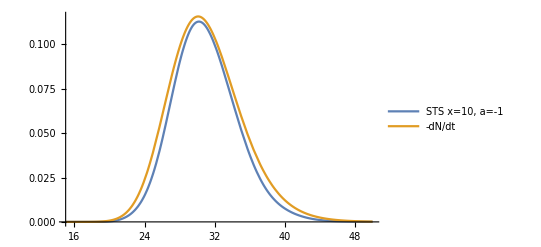

```mathematica
NIntegrate[dnorm10 [t],{t,10, 50}]
```

1.

```mathematica
dndtx20[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+70)^2+2*1*t*(-70))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+70)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-70)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+70)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-70)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+70)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

```mathematica
dn20=FunctionInterpolation[Re[-dndtx20[t]],{t,20,55}]//Quiet
```

InterpolatingFunction[…]

```mathematica
NSolve[A*NIntegrate[dn20[t],{t,20,55}] == 1,A]
```

{{A→0.869468}}

```mathematica
dnorm20 [t_]:= 0.8694675051121641*dn20[t]
```

```mathematica
NIntegrate[dnorm20 [t],{t,20, 55}]
```

1.

```mathematica
Plot[{Abs[sts[20,t]]^2,dnorm20[t]},{t,20,55},PlotLegends->Automatic]
```